```mathematica
f[a_,b_,x_] := a+ b x
```

```mathematica
Manipulate[Plot[a+b x,{x,-1,1}],{a,-1,1},{b,-2,2}]
```

```mathematica
fsmooth[a_,b_,c_,x_, cutoff_] := a + b x + c(x-cutoff)^2
```

```mathematica
Manipulate[Plot[a+b x+c (-cutoff+x)^2,{x,-2.192163740847158,2.192163740847158}],{a,-6.,6.},{b,-2,2},{c,-2,2},{cutoff,-2,2}]
```

```mathematica
f[a,b,x] + fsmooth[a,b,c,x,cutoff]
```

2 a+2 b x+c (-cutoff+x)^2

```mathematica
smoothedffull[a_,b_,c_,x_,cutoff_] :=If[x <cutoff,
f[a,b,x], fsmooth[a,b,c,x,cutoff]]
```

```mathematica
Manipulate[Plot[smoothedffull[a,b,c,x,cutoff],  {x,-3,3}],{a,-6.,6.},{b,-2,2},{c,-2,2},{cutoff,-2,2}]
```

```mathematica
smoothedffullfixed[a_,b_,x_,cutoff_] := smoothedffull[a,b,b^2/(4 cutoff b + 4 a), x, cutoff]
```

```mathematica
Manipulate[Plot[smoothedffullfixed[a,b,x,cutoff],  {x,0,20}, PlotRange->{-10,10}],{a,-6.,6.},{b,-2,2},{cutoff,-2,2}]
```

```mathematica
\
```

```mathematica
smoothedffull[1,1,1,1]
```

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

Hold[smoothedffull[1,1,1^2/(4 1 1+1),1]]

```mathematica
smoothedffull[1,1,1,1]
```

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

```mathematica
Clear[f]
```

```mathematica
p[rs_] = a rs^10 + b rs^8 + c rs^6 + d rs^4+ e rs^2 + f
```

f+e rs^2+d rs^4+c rs^6+b rs^8+a rs^10

```mathematica
p'[rs]
```

```mathematica
e+2 d rs+3 c rs^2+4 b rs^3+5 a rs^4
Clear[α,β,γ]
```

e+2 d rs+3 c rs^2+4 b rs^3+5 a rs^4

```mathematica
replacementrules = Solve[p[rs] ==0 && p'[rs]== 0 && p''[rs]==0&& p[rc(1-δ)] ==α&& p'[rc(1-δ)]== β && p''[rc(1-δ)] == γ, {a,b,c,d,e,f}]
```

{{a→-((1. (-1. ((1) 1-1) (-1. (48. rs^5 (-24. rc rs^2 (1.-1. δ)+8. rc^3 (1.-1. δ)^3)-16. rs^3 (-60. rc rs^4 (1.-1. δ)+12. rc^5 (1.-1. δ)^5)) (0.-16. rs^3 (0.-(7.5 coeff δ^0.5)/rc^2))+(48. rs^5 (-24. rs^2+24. rc^2 (1.-1)^2)-16. rs^3 (-60. rs^4+60. rc^4 1^4)) (0.-1))+1))/((-1. (48. rs^5 (-24. rc rs^2 (1.-1. δ)+8. rc^3 (1.-1. δ)^3)-16. rs^3 (-60. rc rs^4 (1.-1. δ)+12. rc^5 (1.-1. δ)^5)) (96. rs^7 (-24. rs^2+24. rc^2 (1.-1. δ)^2)-16. rs^3 (-112. rs^6+112. rc^6 (1.-1. δ)^6))+(48. rs^5 (-24. rs^2+24. rc^2 (1)^2)-16. rs^3 (-60. rs^4+1)) (1-1)) (1)-1. (1) (1))),b→-1,3,f→1}}
 |  |  |  |

```mathematica
smoothingpolynomial[x_, rc_, rs_, coeff_, δ_] =(p[x]/. replacementrules)[[1]]
```

10+x^2 ((0.375 coeff rs^4 δ^0.5)/(rc^2 (1. rc^4-1.2 rc^2 rs^2+0.2 rs^4-4. rc^4 δ+2.4 rc^2 rs^2 δ+6. rc^4 δ^2-1.2 rc^2 rs^2 δ^2-4. rc^4 δ^3+1. rc^4 δ^4))+1/1+(1. 1 (-1. (1-1) (-1. (48. rs^5 (-24. rc rs^2 (1.-1. δ)+8. rc^3 (1)^3)-16. rs^3 (1+1)) (0.-16. rs^3 (0.-(7.5 coeff δ^22)/rc^2))+1)+1))/((-1. (48. rs^5 (-24. rc rs^2 (1.-1. δ)+8. rc^3 1^3)-1) (96. rs^7 (-24. rs^2+24. rc^2 (1.-1. δ)^2)-16. rs^3 (-112. rs^6+112. rc^6 (1.-1. δ)^6))+(1) 1) 1-1))
 |  |  |  |

```mathematica
p[x]
```

f+e x+d x^2+c x^3+b x^4+a x^5

```mathematica
replacementrules
```

{{a→(1.875 (1. coeff rc^7 δ^0.5-7. coeff rc^6 rs δ^0.5+21. coeff rc^5 rs^2 δ^0.5-35. coeff rc^4 rs^3 δ^0.5+35. coeff rc^3 rs^4 δ^0.5-21. coeff rc^2 rs^5 δ^0.5+7. coeff rc rs^6 δ^0.5-1. coeff rs^7 δ^0.5+4. coeff rc^7 δ^1.5-24. coeff rc^6 rs δ^1.5+60. coeff rc^5 rs^2 δ^1.5-80. coeff rc^4 rs^3 δ^1.5+60. coeff rc^3 rs^4 δ^1.5-24. coeff rc^2 rs^5 δ^1.5+4. coeff rc rs^6 δ^1.5+3.2 coeff rc^7 δ^2.5-16. coeff rc^6 rs δ^2.5+32. coeff rc^5 rs^2 δ^2.5-32. coeff rc^4 rs^3 δ^2.5+16. coeff rc^3 rs^4 δ^2.5-3.2 coeff rc^2 rs^5 δ^2.5))/(rc^2 (1. rc^10-10. rc^9 rs+45. rc^8 rs^2-120. rc^7 rs^3+210. rc^6 rs^4-252. rc^5 rs^5+210. rc^4 rs^6-120. rc^3 rs^7+45. rc^2 rs^8-10. rc rs^9+1. rs^10)),b→-((3.75 (1. coeff rc^12 δ^0.5-9.5 coeff rc^11 rs δ^0.5+38.5 coeff rc^10 rs^2 δ^0.5-82.5 coeff rc^9 rs^3 δ^0.5+82.5 coeff rc^8 rs^4 δ^0.5+33. coeff rc^7 rs^5 δ^0.5-231. coeff rc^6 rs^6 δ^0.5+363. coeff rc^5 rs^7 δ^0.5-330. coeff rc^4 rs^8 δ^0.5+192.5 coeff rc^3 rs^9 δ^0.5-71.5 coeff rc^2 rs^10 δ^0.5+15.5 coeff rc rs^11 δ^0.5-1.5 coeff rs^12 δ^0.5+4.66667 coeff rc^12 δ^1.5-41.3333 coeff rc^11 rs δ^1.5+156.667 coeff rc^10 rs^2 δ^1.5-320. coeff rc^9 rs^3 δ^1.5+340. coeff rc^8 rs^4 δ^1.5-56. coeff rc^7 rs^5 δ^1.5-364. coeff rc^6 rs^6 δ^1.5+560. coeff rc^5 rs^7 δ^1.5-430. coeff rc^4 rs^8 δ^1.5+193.333 coeff rc^3 rs^9 δ^1.5-48.6667 coeff rc^2 rs^10 δ^1.5+5.33333 coeff rc rs^11 δ^1.5+4. coeff rc^12 δ^2.5-32. coeff rc^11 rs δ^2.5+108. coeff rc^10 rs^2 δ^2.5-192. coeff rc^9 rs^3 δ^2.5+168. coeff rc^8 rs^4 δ^2.5-168. coeff rc^6 rs^6 δ^2.5+192. coeff rc^5 rs^7 δ^2.5-108. coeff rc^4 rs^8 δ^2.5+32. coeff rc^3 rs^9 δ^2.5-4. coeff rc^2 rs^10 δ^2.5))/(rc^2 (1. rc^4-4. rc^3 rs+6. rc^2 rs^2-4. rc rs^3+1. rs^4) (1. rc^10-10. rc^9 rs+45. rc^8 rs^2-120. rc^7 rs^3+210. rc^6 rs^4-252. rc^5 rs^5+210. rc^4 rs^6-120. rc^3 rs^7+45. rc^2 rs^8-10. rc rs^9+1. rs^10))),c→(1.875 (1. coeff rc^14 δ^0.5-6. coeff rc^13 rs δ^0.5-3. coeff rc^12 rs^2 δ^0.5+140. coeff rc^11 rs^3 δ^0.5-627. coeff rc^10 rs^4 δ^0.5+1518. coeff rc^9 rs^5 δ^0.5-2343. coeff rc^8 rs^6 δ^0.5+2376. coeff rc^7 rs^7 δ^0.5-1485. coeff rc^6 rs^8 δ^0.5+374. coeff rc^5 rs^9 δ^0.5+231. coeff rc^4 rs^10 δ^0.5-276. coeff rc^3 rs^11 δ^0.5+127. coeff rc^2 rs^12 δ^0.5-30. coeff rc rs^13 δ^0.5+3. coeff rs^14 δ^0.5+5.33333 coeff rc^14 δ^1.5-32. coeff rc^13 rs δ^1.5+8. coeff rc^12 rs^2 δ^1.5+498.667 coeff rc^11 rs^3 δ^1.5-2200. coeff rc^10 rs^4 δ^1.5+5016. coeff rc^9 rs^5 δ^1.5-7216. coeff rc^8 rs^6 δ^1.5+6864. coeff rc^7 rs^7 δ^1.5-4224. coeff rc^6 rs^8 δ^1.5+1466.67 coeff rc^5 rs^9 δ^1.5-88. coeff rc^4 rs^10 δ^1.5-152. coeff rc^3 rs^11 δ^1.5+61.3333 coeff rc^2 rs^12 δ^1.5-8. coeff rc rs^13 δ^1.5+5.33333 coeff rc^14 δ^2.5-32. coeff rc^13 rs δ^2.5+32. coeff rc^12 rs^2 δ^2.5+266.667 coeff rc^11 rs^3 δ^2.5-1200. coeff rc^10 rs^4 δ^2.5+2496. coeff rc^9 rs^5 δ^2.5-3136. coeff rc^8 rs^6 δ^2.5+2496. coeff rc^7 rs^7 δ^2.5-1200. coeff rc^6 rs^8 δ^2.5+266.667 coeff rc^5 rs^9 δ^2.5+32. coeff rc^4 rs^10 δ^2.5-32. coeff rc^3 rs^11 δ^2.5+5.33333 coeff rc^2 rs^12 δ^2.5))/(rc^2 (1. rc-1. rs) (1. rc^4-4. rc^3 rs+6. rc^2 rs^2-4. rc rs^3+1. rs^4) (1. rc^10-10. rc^9 rs+45. rc^8 rs^2-120. rc^7 rs^3+210. rc^6 rs^4-252. rc^5 rs^5+210. rc^4 rs^6-120. rc^3 rs^7+45. rc^2 rs^8-10. rc rs^9+1. rs^10)),d→-((5.625 (1. coeff rc^14 rs δ^0.5-10. coeff rc^13 rs^2 δ^0.5+42.3333 coeff rc^12 rs^3 δ^0.5-92. coeff rc^11 rs^4 δ^0.5+77. coeff rc^10 rs^5 δ^0.5+124.667 coeff rc^9 rs^6 δ^0.5-495. coeff rc^8 rs^7 δ^0.5+792. coeff rc^7 rs^8 δ^0.5-781. coeff rc^6 rs^9 δ^0.5+506. coeff rc^5 rs^10 δ^0.5-209. coeff rc^4 rs^11 δ^0.5+46.6667 coeff rc^3 rs^12 δ^0.5-1. coeff rc^2 rs^13 δ^0.5-2. coeff rc rs^14 δ^0.5+0.333333 coeff rs^15 δ^0.5+5.33333 coeff rc^14 rs δ^1.5-50.6667 coeff rc^13 rs^2 δ^1.5+205.333 coeff rc^12 rs^3 δ^1.5-440. coeff rc^11 rs^4 δ^1.5+440. coeff rc^10 rs^5 δ^1.5+176. coeff rc^9 rs^6 δ^1.5-1232. coeff rc^8 rs^7 δ^1.5+1936. coeff rc^7 rs^8 δ^1.5-1760. coeff rc^6 rs^9 δ^1.5+1026.67 coeff rc^5 rs^10 δ^1.5-381.333 coeff rc^4 rs^11 δ^1.5+82.6667 coeff rc^3 rs^12 δ^1.5-8. coeff rc^2 rs^13 δ^1.5+5.33333 coeff rc^14 rs δ^2.5-48. coeff rc^13 rs^2 δ^2.5+186.667 coeff rc^12 rs^3 δ^2.5-400. coeff rc^11 rs^4 δ^2.5+480. coeff rc^10 rs^5 δ^2.5-224. coeff rc^9 rs^6 δ^2.5-224. coeff rc^8 rs^7 δ^2.5+480. coeff rc^7 rs^8 δ^2.5-400. coeff rc^6 rs^9 δ^2.5+186.667 coeff rc^5 rs^10 δ^2.5-48. coeff rc^4 rs^11 δ^2.5+5.33333 coeff rc^3 rs^12 δ^2.5))/(rc^2 (1. rc-1. rs) (1. rc^4-4. rc^3 rs+6. rc^2 rs^2-4. rc rs^3+1. rs^4) (1. rc^10-10. rc^9 rs+45. rc^8 rs^2-120. rc^7 rs^3+210. rc^6 rs^4-252. rc^5 rs^5+210. rc^4 rs^6-120. rc^3 rs^7+45. rc^2 rs^8-10. rc rs^9+1. rs^10))),e→(5.625 (1. coeff rc^13 rs^2 δ^0.5-11.3333 coeff rc^12 rs^3 δ^0.5+58. coeff rc^11 rs^4 δ^0.5-176. coeff rc^10 rs^5 δ^0.5+348.333 coeff rc^9 rs^6 δ^0.5-462. coeff rc^8 rs^7 δ^0.5+396. coeff rc^7 rs^8 δ^0.5-176. coeff rc^6 rs^9 δ^0.5-33. coeff rc^5 rs^10 δ^0.5+110. coeff rc^4 rs^11 δ^0.5-80.6667 coeff rc^3 rs^12 δ^0.5+32. coeff rc^2 rs^13 δ^0.5-7. coeff rc rs^14 δ^0.5+0.666667 coeff rs^15 δ^0.5+5.33333 coeff rc^13 rs^2 δ^1.5-56.8889 coeff rc^12 rs^3 δ^1.5+273.333 coeff rc^11 rs^4 δ^1.5-777.333 coeff rc^10 rs^5 δ^1.5+1442.22 coeff rc^9 rs^6 δ^1.5-1804. coeff rc^8 rs^7 δ^1.5+1496. coeff rc^7 rs^8 δ^1.5-733.333 coeff rc^6 rs^9 δ^1.5+88. coeff rc^5 rs^10 δ^1.5+146.667 coeff rc^4 rs^11 δ^1.5-112.444 coeff rc^3 rs^12 δ^1.5+38.6667 coeff rc^2 rs^13 δ^1.5-6.66667 coeff rc rs^14 δ^1.5+0.444444 coeff rs^15 δ^1.5+5.33333 coeff rc^13 rs^2 δ^2.5-53.3333 coeff rc^12 rs^3 δ^2.5+240. coeff rc^11 rs^4 δ^2.5-640. coeff rc^10 rs^5 δ^2.5+1120. coeff rc^9 rs^6 δ^2.5-1344. coeff rc^8 rs^7 δ^2.5+1120. coeff rc^7 rs^8 δ^2.5-640. coeff rc^6 rs^9 δ^2.5+240. coeff rc^5 rs^10 δ^2.5-53.3333 coeff rc^4 rs^11 δ^2.5+5.33333 coeff rc^3 rs^12 δ^2.5))/(rc (1. rc-1. rs) (1. rc^4-4. rc^3 rs+6. rc^2 rs^2-4. rc rs^3+1. rs^4) (1. rc^10-10. rc^9 rs+45. rc^8 rs^2-120. rc^7 rs^3+210. rc^6 rs^4-252. rc^5 rs^5+210. rc^4 rs^6-120. rc^3 rs^7+45. rc^2 rs^8-10. rc rs^9+1. rs^10)),f→-((1.875 (1. coeff rc^12 rs^3 δ^0.5-12. coeff rc^11 rs^4 δ^0.5+66. coeff rc^10 rs^5 δ^0.5-220. coeff rc^9 rs^6 δ^0.5+495. coeff rc^8 rs^7 δ^0.5-792. coeff rc^7 rs^8 δ^0.5+924. coeff rc^6 rs^9 δ^0.5-792. coeff rc^5 rs^10 δ^0.5+495. coeff rc^4 rs^11 δ^0.5-220. coeff rc^3 rs^12 δ^0.5+66. coeff rc^2 rs^13 δ^0.5-12. coeff rc rs^14 δ^0.5+1. coeff rs^15 δ^0.5+5.33333 coeff rc^12 rs^3 δ^1.5-60. coeff rc^11 rs^4 δ^1.5+308. coeff rc^10 rs^5 δ^1.5-953.333 coeff rc^9 rs^6 δ^1.5+1980. coeff rc^8 rs^7 δ^1.5-2904. coeff rc^7 rs^8 δ^1.5+3080. coeff rc^6 rs^9 δ^1.5-2376. coeff rc^5 rs^10 δ^1.5+1320. coeff rc^4 rs^11 δ^1.5-513.333 coeff rc^3 rs^12 δ^1.5+132. coeff rc^2 rs^13 δ^1.5-20. coeff rc rs^14 δ^1.5+1.33333 coeff rs^15 δ^1.5+5.33333 coeff rc^12 rs^3 δ^2.5-56. coeff rc^11 rs^4 δ^2.5+267.2 coeff rc^10 rs^5 δ^2.5-765.333 coeff rc^9 rs^6 δ^2.5+1464. coeff rc^8 rs^7 δ^2.5-1968. coeff rc^7 rs^8 δ^2.5+1904. coeff rc^6 rs^9 δ^2.5-1334.4 coeff rc^5 rs^10 δ^2.5+672. coeff rc^4 rs^11 δ^2.5-237.333 coeff rc^3 rs^12 δ^2.5+56. coeff rc^2 rs^13 δ^2.5-8. coeff rc rs^14 δ^2.5+0.533333 coeff rs^15 δ^2.5))/((1. rc-1. rs) (1. rc^4-4. rc^3 rs+6. rc^2 rs^2-4. rc rs^3+1. rs^4) (1. rc^10-10. rc^9 rs+45. rc^8 rs^2-120. rc^7 rs^3+210. rc^6 rs^4-252. rc^5 rs^5+210. rc^4 rs^6-120. rc^3 rs^7+45. rc^2 rs^8-10. rc rs^9+1. rs^10)))}}

```mathematica
{{a->-(-12 α+6 rc β-6 rs β-rc^2 γ+2 rc rs γ-rs^2 γ)/(2 (rc-rs)^5),b->-(30 rc α+30 rs α-14 rc^2 β-2 rc rs β+16 rs^2 β+2 rc^3 γ-rc^2 rs γ-4 rc rs^2 γ+3 rs^3 γ)/(2 (rc-rs)^5),c->-1/(2 (rc-rs)^5)(-20 rc^2 α-80 rc rs α-20 rs^2 α+8 rc^3 β+32 rc^2 rs β-28 rc rs^2 β-12 rs^3 β-rc^4 γ-4 rc^3 rs γ+8 rc^2 rs^2 γ-3 rs^4 γ),d->-(60 rc^2 rs α+60 rc rs^2 α-24 rc^3 rs β-12 rc^2 rs^2 β+36 rc rs^3 β+3 rc^4 rs γ-8 rc^2 rs^3 γ+4 rc rs^4 γ+rs^5 γ)/(2 (rc-rs)^5),e->-(-60 rc^2 rs^2 α+24 rc^3 rs^2 β-16 rc^2 rs^3 β-10 rc rs^4 β+2 rs^5 β-3 rc^4 rs^2 γ+4 rc^3 rs^3 γ+rc^2 rs^4 γ-2 rc rs^5 γ)/(2 (rc-rs)^5),f->-(20 rc^2 rs^3 α-10 rc rs^4 α+2 rs^5 α-8 rc^3 rs^3 β+10 rc^2 rs^4 β-2 rc rs^5 β+rc^4 rs^3 γ-2 rc^3 rs^4 γ+rc^2 rs^5 γ)/(2 (rc-rs)^5)}}
```

```mathematica
%60/.Rule->Equal
```

{{a==-((1. (-1. (-1. (24. rc^2-24. rs^2) (-6. rs (-2. (1. rc-1. rs) rs+1. (1. rc^2-1. rs^2))+2. (-3. (1. rc-1. rs) rs^2+1. (1. rc^3-1. rs^3)))+(12. rc-12. rs) (-12. rs^2 (-2. (1. rc-1. rs) rs+1. (1. rc^2-1. rs^2))+2. (-4. (1. rc-1. rs) rs^3+1. (1. rc^4-1. rs^4)))) (-1. (-6. (2. rc-2. rs) rs+2. (3. rc^2-3. rs^2)) (0.-(7.5 coeff (1.-(1. (rc-1. rc δ))/rc)^0.5)/rc^2)+(12. rc-12. rs) (0.+2. (0.+(2.5 coeff (1.-(1. (rc-1. rc δ))/rc)^1.5)/rc)))+(-48. rc^4+192. rc^3 rs-288. rc^2 rs^2+192. rc rs^3-48. rs^4) (-1. (-6. rs (-2. (1. rc-1. rs) rs+1. (1. rc^2-1. rs^2))+2. (-3. (1. rc-1. rs) rs^2+1. (1. rc^3-1. rs^3))) (0.-(7.5 coeff (1.-(1. (rc-1. rc δ))/rc)^0.5)/rc^2)+(12. rc-12. rs) (0.+2. (0.+1. (0.-1. coeff (1.-(1. (rc-1. rc δ))/rc)^2.5))))))/(-192. rc^10+1920. rc^9 rs-8640. rc^8 rs^2+23040. rc^7 rs^3-40320. rc^6 rs^4+48384. rc^5 rs^5-40320. rc^4 rs^6+23040. rc^3 rs^7-8640. rc^2 rs^8+1920. rc rs^9-192. rs^10)),b==-((3.75 (1. coeff rc^12 (1.-(1. (rc-1. rc δ))/rc)^0.5-9.5 coeff rc^11 rs (1.-(1. (rc-1. rc δ))/rc)^0.5+38.5 coeff rc^10 rs^2 (1.-(1. (rc-1. rc δ))/rc)^0.5-82.5 coeff rc^9 rs^3 (1.-(1. (rc-1. rc δ))/rc)^0.5+82.5 coeff rc^8 rs^4 (1.-(1. (rc-1. rc δ))/rc)^0.5+33. coeff rc^7 rs^5 (1.-(1. (rc-1. rc δ))/rc)^0.5-231. coeff rc^6 rs^6 (1.-(1. (rc-1. rc δ))/rc)^0.5+363. coeff rc^5 rs^7 (1.-(1. (rc-1. rc δ))/rc)^0.5-330. coeff rc^4 rs^8 (1.-(1. (rc-1. rc δ))/rc)^0.5+192.5 coeff rc^3 rs^9 (1.-(1. (rc-1. rc δ))/rc)^0.5-71.5 coeff rc^2 rs^10 (1.-(1. (rc-1. rc δ))/rc)^0.5+15.5 coeff rc rs^11 (1.-(1. (rc-1. rc δ))/rc)^0.5-1.5 coeff rs^12 (1.-(1. (rc-1. rc δ))/rc)^0.5+4.66667 coeff rc^12 (1.-(1. (rc-1. rc δ))/rc)^1.5-41.3333 coeff rc^11 rs (1.-(1. (rc-1. rc δ))/rc)^1.5+156.667 coeff rc^10 rs^2 (1.-(1. (rc-1. rc δ))/rc)^1.5-320. coeff rc^9 rs^3 (1.-(1. (rc-1. rc δ))/rc)^1.5+340. coeff rc^8 rs^4 (1.-(1. (rc-1. rc δ))/rc)^1.5-56. coeff rc^7 rs^5 (1.-(1. (rc-1. rc δ))/rc)^1.5-364. coeff rc^6 rs^6 (1.-(1. (rc-1. rc δ))/rc)^1.5+560. coeff rc^5 rs^7 (1.-(1. (rc-1. rc δ))/rc)^1.5-430. coeff rc^4 rs^8 (1.-(1. (rc-1. rc δ))/rc)^1.5+193.333 coeff rc^3 rs^9 (1.-(1. (rc-1. rc δ))/rc)^1.5-48.6667 coeff rc^2 rs^10 (1.-(1. (rc-1. rc δ))/rc)^1.5+5.33333 coeff rc rs^11 (1.-(1. (rc-1. rc δ))/rc)^1.5+4. coeff rc^12 (1.-(1. (rc-1. rc δ))/rc)^2.5-32. coeff rc^11 rs (1.-(1. (rc-1. rc δ))/rc)^2.5+108. coeff rc^10 rs^2 (1.-(1. (rc-1. rc δ))/rc)^2.5-192. coeff rc^9 rs^3 (1.-(1. (rc-1. rc δ))/rc)^2.5+168. coeff rc^8 rs^4 (1.-(1. (rc-1. rc δ))/rc)^2.5-168. coeff rc^6 rs^6 (1.-(1. (rc-1. rc δ))/rc)^2.5+192. coeff rc^5 rs^7 (1.-(1. (rc-1. rc δ))/rc)^2.5-108. coeff rc^4 rs^8 (1.-(1. (rc-1. rc δ))/rc)^2.5+32. coeff rc^3 rs^9 (1.-(1. (rc-1. rc δ))/rc)^2.5-4. coeff rc^2 rs^10 (1.-(1. (rc-1. rc δ))/rc)^2.5))/(rc^2 (1. rc^4-4. rc^3 rs+6. rc^2 rs^2-4. rc rs^3+1. rs^4) (1. rc^10-10. rc^9 rs+45. rc^8 rs^2-120. rc^7 rs^3+210. rc^6 rs^4-252. rc^5 rs^5+210. rc^4 rs^6-120. rc^3 rs^7+45. rc^2 rs^8-10. rc rs^9+1. rs^10))),c==(1.875 (1. coeff rc^14 (1.-(1. (rc-1. rc δ))/rc)^0.5-6. coeff rc^13 rs (1.-(1. (rc-1. rc δ))/rc)^0.5-3. coeff rc^12 rs^2 (1.-(1. (rc-1. rc δ))/rc)^0.5+140. coeff rc^11 rs^3 (1.-(1. (rc-1. rc δ))/rc)^0.5-627. coeff rc^10 rs^4 (1.-(1. (rc-1. rc δ))/rc)^0.5+1518. coeff rc^9 rs^5 (1.-(1. (rc-1. rc δ))/rc)^0.5-2343. coeff rc^8 rs^6 (1.-(1. (rc-1. rc δ))/rc)^0.5+2376. coeff rc^7 rs^7 (1.-(1. (rc-1. rc δ))/rc)^0.5-1485. coeff rc^6 rs^8 (1.-(1. (rc-1. rc δ))/rc)^0.5+374. coeff rc^5 rs^9 (1.-(1. (rc-1. rc δ))/rc)^0.5+231. coeff rc^4 rs^10 (1.-(1. (rc-1. rc δ))/rc)^0.5-276. coeff rc^3 rs^11 (1.-(1. (rc-1. rc δ))/rc)^0.5+127. coeff rc^2 rs^12 (1.-(1. (rc-1. rc δ))/rc)^0.5-30. coeff rc rs^13 (1.-(1. (rc-1. rc δ))/rc)^0.5+3. coeff rs^14 (1.-(1. (rc-1. rc δ))/rc)^0.5+5.33333 coeff rc^14 (1.-(1. (rc-1. rc δ))/rc)^1.5-32. coeff rc^13 rs (1.-(1. (rc-1. rc δ))/rc)^1.5+8. coeff rc^12 rs^2 (1.-(1. (rc-1. rc δ))/rc)^1.5+498.667 coeff rc^11 rs^3 (1.-(1. (rc-1. rc δ))/rc)^1.5-2200. coeff rc^10 rs^4 (1.-(1. (rc-1. rc δ))/rc)^1.5+5016. coeff rc^9 rs^5 (1.-(1. (rc-1. rc δ))/rc)^1.5-7216. coeff rc^8 rs^6 (1.-(1. (rc-1. rc δ))/rc)^1.5+6864. coeff rc^7 rs^7 (1.-(1. (rc-1. rc δ))/rc)^1.5-4224. coeff rc^6 rs^8 (1.-(1. (rc-1. rc δ))/rc)^1.5+1466.67 coeff rc^5 rs^9 (1.-(1. (rc-1. rc δ))/rc)^1.5-88. coeff rc^4 rs^10 (1.-(1. (rc-1. rc δ))/rc)^1.5-152. coeff rc^3 rs^11 (1.-(1. (rc-1. rc δ))/rc)^1.5+61.3333 coeff rc^2 rs^12 (1.-(1. (rc-1. rc δ))/rc)^1.5-8. coeff rc rs^13 (1.-(1. (rc-1. rc δ))/rc)^1.5+5.33333 coeff rc^14 (1.-(1. (rc-1. rc δ))/rc)^2.5-32. coeff rc^13 rs (1.-(1. (rc-1. rc δ))/rc)^2.5+32. coeff rc^12 rs^2 (1.-(1. (rc-1. rc δ))/rc)^2.5+266.667 coeff rc^11 rs^3 (1.-(1. (rc-1. rc δ))/rc)^2.5-1200. coeff rc^10 rs^4 (1.-(1. (rc-1. rc δ))/rc)^2.5+2496. coeff rc^9 rs^5 (1.-(1. (rc-1. rc δ))/rc)^2.5-3136. coeff rc^8 rs^6 (1.-(1. (rc-1. rc δ))/rc)^2.5+2496. coeff rc^7 rs^7 (1.-(1. (rc-1. rc δ))/rc)^2.5-1200. coeff rc^6 rs^8 (1.-(1. (rc-1. rc δ))/rc)^2.5+266.667 coeff rc^5 rs^9 (1.-(1. (rc-1. rc δ))/rc)^2.5+32. coeff rc^4 rs^10 (1.-(1. (rc-1. rc δ))/rc)^2.5-32. coeff rc^3 rs^11 (1.-(1. (rc-1. rc δ))/rc)^2.5+5.33333 coeff rc^2 rs^12 (1.-(1. (rc-1. rc δ))/rc)^2.5))/(rc^2 (1. rc-1. rs) (1. rc^4-4. rc^3 rs+6. rc^2 rs^2-4. rc rs^3+1. rs^4) (1. rc^10-10. rc^9 rs+45. rc^8 rs^2-120. rc^7 rs^3+210. rc^6 rs^4-252. rc^5 rs^5+210. rc^4 rs^6-120. rc^3 rs^7+45. rc^2 rs^8-10. rc rs^9+1. rs^10)),d==-((5.625 (1. coeff rc^14 rs (1.-(1. (rc-1. rc δ))/rc)^0.5-10. coeff rc^13 rs^2 (1.-(1. (rc-1. rc δ))/rc)^0.5+42.3333 coeff rc^12 rs^3 (1.-(1. (rc-1. rc δ))/rc)^0.5-92. coeff rc^11 rs^4 (1.-(1. (rc-1. rc δ))/rc)^0.5+77. coeff rc^10 rs^5 (1.-(1. (rc-1. rc δ))/rc)^0.5+124.667 coeff rc^9 rs^6 (1.-(1. (rc-1. rc δ))/rc)^0.5-495. coeff rc^8 rs^7 (1.-(1. (rc-1. rc δ))/rc)^0.5+792. coeff rc^7 rs^8 (1.-(1. (rc-1. rc δ))/rc)^0.5-781. coeff rc^6 rs^9 (1.-(1. (rc-1. rc δ))/rc)^0.5+506. coeff rc^5 rs^10 (1.-(1. (rc-1. rc δ))/rc)^0.5-209. coeff rc^4 rs^11 (1.-(1. (rc-1. rc δ))/rc)^0.5+46.6667 coeff rc^3 rs^12 (1.-(1. (rc-1. rc δ))/rc)^0.5-1. coeff rc^2 rs^13 (1.-(1. (rc-1. rc δ))/rc)^0.5-2. coeff rc rs^14 (1.-(1. (rc-1. rc δ))/rc)^0.5+0.333333 coeff rs^15 (1.-(1. (rc-1. rc δ))/rc)^0.5+5.33333 coeff rc^14 rs (1.-(1. (rc-1. rc δ))/rc)^1.5-50.6667 coeff rc^13 rs^2 (1.-(1. (rc-1. rc δ))/rc)^1.5+205.333 coeff rc^12 rs^3 (1.-(1. (rc-1. rc δ))/rc)^1.5-440. coeff rc^11 rs^4 (1.-(1. (rc-1. rc δ))/rc)^1.5+440. coeff rc^10 rs^5 (1.-(1. (rc-1. rc δ))/rc)^1.5+176. coeff rc^9 rs^6 (1.-(1. (rc-1. rc δ))/rc)^1.5-1232. coeff rc^8 rs^7 (1.-(1. (rc-1. rc δ))/rc)^1.5+1936. coeff rc^7 rs^8 (1.-(1. (rc-1. rc δ))/rc)^1.5-1760. coeff rc^6 rs^9 (1.-(1. (rc-1. rc δ))/rc)^1.5+1026.67 coeff rc^5 rs^10 (1.-(1. (rc-1. rc δ))/rc)^1.5-381.333 coeff rc^4 rs^11 (1.-(1. (rc-1. rc δ))/rc)^1.5+82.6667 coeff rc^3 rs^12 (1.-(1. (rc-1. rc δ))/rc)^1.5-8. coeff rc^2 rs^13 (1.-(1. (rc-1. rc δ))/rc)^1.5+5.33333 coeff rc^14 rs (1.-(1. (rc-1. rc δ))/rc)^2.5-48. coeff rc^13 rs^2 (1.-(1. (rc-1. rc δ))/rc)^2.5+186.667 coeff rc^12 rs^3 (1.-(1. (rc-1. rc δ))/rc)^2.5-400. coeff rc^11 rs^4 (1.-(1. (rc-1. rc δ))/rc)^2.5+480. coeff rc^10 rs^5 (1.-(1. (rc-1. rc δ))/rc)^2.5-224. coeff rc^9 rs^6 (1.-(1. (rc-1. rc δ))/rc)^2.5-224. coeff rc^8 rs^7 (1.-(1. (rc-1. rc δ))/rc)^2.5+480. coeff rc^7 rs^8 (1.-(1. (rc-1. rc δ))/rc)^2.5-400. coeff rc^6 rs^9 (1.-(1. (rc-1. rc δ))/rc)^2.5+186.667 coeff rc^5 rs^10 (1.-(1. (rc-1. rc δ))/rc)^2.5-48. coeff rc^4 rs^11 (1.-(1. (rc-1. rc δ))/rc)^2.5+5.33333 coeff rc^3 rs^12 (1.-(1. (rc-1. rc δ))/rc)^2.5))/(rc^2 (1. rc-1. rs) (1. rc^4-4. rc^3 rs+6. rc^2 rs^2-4. rc rs^3+1. rs^4) (1. rc^10-10. rc^9 rs+45. rc^8 rs^2-120. rc^7 rs^3+210. rc^6 rs^4-252. rc^5 rs^5+210. rc^4 rs^6-120. rc^3 rs^7+45. rc^2 rs^8-10. rc rs^9+1. rs^10))),e==(5.625 (1. coeff rc^13 rs^2 (1.-(1. (rc-1. rc δ))/rc)^0.5-11.3333 coeff rc^12 rs^3 (1.-(1. (rc-1. rc δ))/rc)^0.5+58. coeff rc^11 rs^4 (1.-(1. (rc-1. rc δ))/rc)^0.5-176. coeff rc^10 rs^5 (1.-(1. (rc-1. rc δ))/rc)^0.5+348.333 coeff rc^9 rs^6 (1.-(1. (rc-1. rc δ))/rc)^0.5-462. coeff rc^8 rs^7 (1.-(1. (rc-1. rc δ))/rc)^0.5+396. coeff rc^7 rs^8 (1.-(1. (rc-1. rc δ))/rc)^0.5-176. coeff rc^6 rs^9 (1.-(1. (rc-1. rc δ))/rc)^0.5-33. coeff rc^5 rs^10 (1.-(1. (rc-1. rc δ))/rc)^0.5+110. coeff rc^4 rs^11 (1.-(1. (rc-1. rc δ))/rc)^0.5-80.6667 coeff rc^3 rs^12 (1.-(1. (rc-1. rc δ))/rc)^0.5+32. coeff rc^2 rs^13 (1.-(1. (rc-1. rc δ))/rc)^0.5-7. coeff rc rs^14 (1.-(1. (rc-1. rc δ))/rc)^0.5+0.666667 coeff rs^15 (1.-(1. (rc-1. rc δ))/rc)^0.5+5.33333 coeff rc^13 rs^2 (1.-(1. (rc-1. rc δ))/rc)^1.5-56.8889 coeff rc^12 rs^3 (1.-(1. (rc-1. rc δ))/rc)^1.5+273.333 coeff rc^11 rs^4 (1.-(1. (rc-1. rc δ))/rc)^1.5-777.333 coeff rc^10 rs^5 (1.-(1. (rc-1. rc δ))/rc)^1.5+1442.22 coeff rc^9 rs^6 (1.-(1. (rc-1. rc δ))/rc)^1.5-1804. coeff rc^8 rs^7 (1.-(1. (rc-1. rc δ))/rc)^1.5+1496. coeff rc^7 rs^8 (1.-(1. (rc-1. rc δ))/rc)^1.5-733.333 coeff rc^6 rs^9 (1.-(1. (rc-1. rc δ))/rc)^1.5+88. coeff rc^5 rs^10 (1.-(1. (rc-1. rc δ))/rc)^1.5+146.667 coeff rc^4 rs^11 (1.-(1. (rc-1. rc δ))/rc)^1.5-112.444 coeff rc^3 rs^12 (1.-(1. (rc-1. rc δ))/rc)^1.5+38.6667 coeff rc^2 rs^13 (1.-(1. (rc-1. rc δ))/rc)^1.5-6.66667 coeff rc rs^14 (1.-(1. (rc-1. rc δ))/rc)^1.5+0.444444 coeff rs^15 (1.-(1. (rc-1. rc δ))/rc)^1.5+5.33333 coeff rc^13 rs^2 (1.-(1. (rc-1. rc δ))/rc)^2.5-53.3333 coeff rc^12 rs^3 (1.-(1. (rc-1. rc δ))/rc)^2.5+240. coeff rc^11 rs^4 (1.-(1. (rc-1. rc δ))/rc)^2.5-640. coeff rc^10 rs^5 (1.-(1. (rc-1. rc δ))/rc)^2.5+1120. coeff rc^9 rs^6 (1.-(1. (rc-1. rc δ))/rc)^2.5-1344. coeff rc^8 rs^7 (1.-(1. (rc-1. rc δ))/rc)^2.5+1120. coeff rc^7 rs^8 (1.-(1. (rc-1. rc δ))/rc)^2.5-640. coeff rc^6 rs^9 (1.-(1. (rc-1. rc δ))/rc)^2.5+240. coeff rc^5 rs^10 (1.-(1. (rc-1. rc δ))/rc)^2.5-53.3333 coeff rc^4 rs^11 (1.-(1. (rc-1. rc δ))/rc)^2.5+5.33333 coeff rc^3 rs^12 (1.-(1. (rc-1. rc δ))/rc)^2.5))/(rc (1. rc-1. rs) (1. rc^4-4. rc^3 rs+6. rc^2 rs^2-4. rc rs^3+1. rs^4) (1. rc^10-10. rc^9 rs+45. rc^8 rs^2-120. rc^7 rs^3+210. rc^6 rs^4-252. rc^5 rs^5+210. rc^4 rs^6-120. rc^3 rs^7+45. rc^2 rs^8-10. rc rs^9+1. rs^10)),f==-((1.875 (1. coeff rc^12 rs^3 (1.-(1. (rc-1. rc δ))/rc)^0.5-12. coeff rc^11 rs^4 (1.-(1. (rc-1. rc δ))/rc)^0.5+66. coeff rc^10 rs^5 (1.-(1. (rc-1. rc δ))/rc)^0.5-220. coeff rc^9 rs^6 (1.-(1. (rc-1. rc δ))/rc)^0.5+495. coeff rc^8 rs^7 (1.-(1. (rc-1. rc δ))/rc)^0.5-792. coeff rc^7 rs^8 (1.-(1. (rc-1. rc δ))/rc)^0.5+924. coeff rc^6 rs^9 (1.-(1. (rc-1. rc δ))/rc)^0.5-792. coeff rc^5 rs^10 (1.-(1. (rc-1. rc δ))/rc)^0.5+495. coeff rc^4 rs^11 (1.-(1. (rc-1. rc δ))/rc)^0.5-220. coeff rc^3 rs^12 (1.-(1. (rc-1. rc δ))/rc)^0.5+66. coeff rc^2 rs^13 (1.-(1. (rc-1. rc δ))/rc)^0.5-12. coeff rc rs^14 (1.-(1. (rc-1. rc δ))/rc)^0.5+1. coeff rs^15 (1.-(1. (rc-1. rc δ))/rc)^0.5+5.33333 coeff rc^12 rs^3 (1.-(1. (rc-1. rc δ))/rc)^1.5-60. coeff rc^11 rs^4 (1.-(1. (rc-1. rc δ))/rc)^1.5+308. coeff rc^10 rs^5 (1.-(1. (rc-1. rc δ))/rc)^1.5-953.333 coeff rc^9 rs^6 (1.-(1. (rc-1. rc δ))/rc)^1.5+1980. coeff rc^8 rs^7 (1.-(1. (rc-1. rc δ))/rc)^1.5-2904. coeff rc^7 rs^8 (1.-(1. (rc-1. rc δ))/rc)^1.5+3080. coeff rc^6 rs^9 (1.-(1. (rc-1. rc δ))/rc)^1.5-2376. coeff rc^5 rs^10 (1.-(1. (rc-1. rc δ))/rc)^1.5+1320. coeff rc^4 rs^11 (1.-(1. (rc-1. rc δ))/rc)^1.5-513.333 coeff rc^3 rs^12 (1.-(1. (rc-1. rc δ))/rc)^1.5+132. coeff rc^2 rs^13 (1.-(1. (rc-1. rc δ))/rc)^1.5-20. coeff rc rs^14 (1.-(1. (rc-1. rc δ))/rc)^1.5+1.33333 coeff rs^15 (1.-(1. (rc-1. rc δ))/rc)^1.5+5.33333 coeff rc^12 rs^3 (1.-(1. (rc-1. rc δ))/rc)^2.5-56. coeff rc^11 rs^4 (1.-(1. (rc-1. rc δ))/rc)^2.5+267.2 coeff rc^10 rs^5 (1.-(1. (rc-1. rc δ))/rc)^2.5-765.333 coeff rc^9 rs^6 (1.-(1. (rc-1. rc δ))/rc)^2.5+1464. coeff rc^8 rs^7 (1.-(1. (rc-1. rc δ))/rc)^2.5-1968. coeff rc^7 rs^8 (1.-(1. (rc-1. rc δ))/rc)^2.5+1904. coeff rc^6 rs^9 (1.-(1. (rc-1. rc δ))/rc)^2.5-1334.4 coeff rc^5 rs^10 (1.-(1. (rc-1. rc δ))/rc)^2.5+672. coeff rc^4 rs^11 (1.-(1. (rc-1. rc δ))/rc)^2.5-237.333 coeff rc^3 rs^12 (1.-(1. (rc-1. rc δ))/rc)^2.5+56. coeff rc^2 rs^13 (1.-(1. (rc-1. rc δ))/rc)^2.5-8. coeff rc rs^14 (1.-(1. (rc-1. rc δ))/rc)^2.5+0.533333 coeff rs^15 (1.-(1. (rc-1. rc δ))/rc)^2.5))/((1. rc-1. rs) (1. rc^4-4. rc^3 rs+6. rc^2 rs^2-4. rc rs^3+1. rs^4) (1. rc^10-10. rc^9 rs+45. rc^8 rs^2-120. rc^7 rs^3+210. rc^6 rs^4-252. rc^5 rs^5+210. rc^4 rs^6-120. rc^3 rs^7+45. rc^2 rs^8-10. rc rs^9+1. rs^10)))}}

```mathematica
Simplify[%61]
```

{{a==(coeff (-1.875 rs^7 δ^0.5+rc rs^6 (13.125 δ^0.5+7.5 δ^1.5)+rc^4 rs^3 (-65.625 δ^0.5-150. δ^1.5-60. δ^2.5)+rc^6 rs (-13.125 δ^0.5-45. δ^1.5-30. δ^2.5)+rc^2 rs^5 (-39.375 δ^0.5-45. δ^1.5-6. δ^2.5)+rc^7 (1.875 δ^0.5+7.5 δ^1.5+6. δ^2.5)+rc^3 rs^4 (65.625 δ^0.5+112.5 δ^1.5+30. δ^2.5)+rc^5 rs^2 (39.375 δ^0.5+112.5 δ^1.5+60. δ^2.5)))/(rc^2 (1. rc^10-10. rc^9 rs+45. rc^8 rs^2-120. rc^7 rs^3+210. rc^6 rs^4-252. rc^5 rs^5+210. rc^4 rs^6-120. rc^3 rs^7+45. rc^2 rs^8-10. rc rs^9+1. rs^10)),b==(coeff (5.625 rs^12 δ^0.5+rc rs^11 (-58.125 δ^0.5-20. δ^1.5)+rc^7 rs^5 (-123.75 δ^0.5+210. δ^1.5)+rc^5 rs^7 (-1361.25 δ^0.5-2100. δ^1.5-720. δ^2.5)+rc^8 rs^4 (-309.375 δ^0.5-1275. δ^1.5-630. δ^2.5)+rc^10 rs^2 (-144.375 δ^0.5-587.5 δ^1.5-405. δ^2.5)+rc^3 rs^9 (-721.875 δ^0.5-725. δ^1.5-120. δ^2.5)+rc^12 (-3.75 δ^0.5-17.5 δ^1.5-15. δ^2.5)+rc^2 rs^10 (268.125 δ^0.5+182.5 δ^1.5+15. δ^2.5)+rc^11 rs (35.625 δ^0.5+155. δ^1.5+120. δ^2.5)+rc^4 rs^8 (1237.5 δ^0.5+1612.5 δ^1.5+405. δ^2.5)+rc^6 rs^6 (866.25 δ^0.5+1365. δ^1.5+630. δ^2.5)+rc^9 rs^3 (309.375 δ^0.5+1200. δ^1.5+720. δ^2.5)))/(rc^2 (1. rc^4-4. rc^3 rs+6. rc^2 rs^2-4. rc rs^3+1. rs^4) (1. rc^10-10. rc^9 rs+45. rc^8 rs^2-120. rc^7 rs^3+210. rc^6 rs^4-252. rc^5 rs^5+210. rc^4 rs^6-120. rc^3 rs^7+45. rc^2 rs^8-10. rc rs^9+1. rs^10)),c==(coeff (5.625 rs^14 δ^0.5+rc rs^13 (-56.25 δ^0.5-15. δ^1.5)+rc^8 rs^6 (-4393.13 δ^0.5-13530. δ^1.5-5880. δ^2.5)+rc^6 rs^8 (-2784.38 δ^0.5-7920. δ^1.5-2250. δ^2.5)+rc^10 rs^4 (-1175.63 δ^0.5-4125. δ^1.5-2250. δ^2.5)+rc^3 rs^11 (-517.5 δ^0.5-285. δ^1.5-60. δ^2.5)+rc^13 rs (-11.25 δ^0.5-60. δ^1.5-60. δ^2.5)+rc^14 (1.875 δ^0.5+10. δ^1.5+10. δ^2.5)+rc^2 rs^12 (238.125 δ^0.5+115. δ^1.5+10. δ^2.5)+rc^4 rs^10 (433.125 δ^0.5-165. δ^1.5+60. δ^2.5)+rc^12 rs^2 (-5.625 δ^0.5+15. δ^1.5+60. δ^2.5)+rc^11 rs^3 (262.5 δ^0.5+935. δ^1.5+500. δ^2.5)+rc^5 rs^9 (701.25 δ^0.5+2750. δ^1.5+500. δ^2.5)+rc^9 rs^5 (2846.25 δ^0.5+9405. δ^1.5+4680. δ^2.5)+rc^7 rs^7 (4455. δ^0.5+12870. δ^1.5+4680. δ^2.5)))/(rc^2 (1. rc-1. rs) (1. rc^4-4. rc^3 rs+6. rc^2 rs^2-4. rc rs^3+1. rs^4) (1. rc^10-10. rc^9 rs+45. rc^8 rs^2-120. rc^7 rs^3+210. rc^6 rs^4-252. rc^5 rs^5+210. rc^4 rs^6-120. rc^3 rs^7+45. rc^2 rs^8-10. rc rs^9+1. rs^10)),d==(coeff rs (11.25 rc rs^13 δ^0.5-1.875 rs^14 δ^0.5+rc^2 rs^12 (5.625 δ^0.5+45. δ^1.5)+rc^7 rs^7 (-4455. δ^0.5-10890. δ^1.5-2700. δ^2.5)+rc^10 rs^4 (-433.125 δ^0.5-2475. δ^1.5-2700. δ^2.5)+rc^5 rs^9 (-2846.25 δ^0.5-5775. δ^1.5-1050. δ^2.5)+rc^12 rs^2 (-238.125 δ^0.5-1155. δ^1.5-1050. δ^2.5)+rc^3 rs^11 (-262.5 δ^0.5-465. δ^1.5-30. δ^2.5)+rc^14 (-5.625 δ^0.5-30. δ^1.5-30. δ^2.5)+rc^13 rs (56.25 δ^0.5+285. δ^1.5+270. δ^2.5)+rc^4 rs^10 (1175.63 δ^0.5+2145. δ^1.5+270. δ^2.5)+rc^9 rs^5 (-701.25 δ^0.5-990. δ^1.5+1260. δ^2.5)+rc^8 rs^6 (2784.38 δ^0.5+6930. δ^1.5+1260. δ^2.5)+rc^11 rs^3 (517.5 δ^0.5+2475. δ^1.5+2250. δ^2.5)+rc^6 rs^8 (4393.13 δ^0.5+9900. δ^1.5+2250. δ^2.5)))/(rc^2 (1. rc-1. rs) (1. rc^4-4. rc^3 rs+6. rc^2 rs^2-4. rc rs^3+1. rs^4) (1. rc^10-10. rc^9 rs+45. rc^8 rs^2-120. rc^7 rs^3+210. rc^6 rs^4-252. rc^5 rs^5+210. rc^4 rs^6-120. rc^3 rs^7+45. rc^2 rs^8-10. rc rs^9+1. rs^10)),e==(coeff rs^2 (rc rs^12 (-39.375 δ^0.5-37.5 δ^1.5)+rs^13 (3.75 δ^0.5+2.5 δ^1.5)+rc^2 rs^11 (180. δ^0.5+217.5 δ^1.5)+rc^8 rs^5 (-2598.75 δ^0.5-10147.5 δ^1.5-7560. δ^2.5)+rc^10 rs^3 (-990. δ^0.5-4372.5 δ^1.5-3600. δ^2.5)+rc^6 rs^7 (-990. δ^0.5-4125. δ^1.5-3600. δ^2.5)+rc^12 rs (-63.75 δ^0.5-320. δ^1.5-300. δ^2.5)+rc^4 rs^9 (618.75 δ^0.5+825. δ^1.5-300. δ^2.5)+rc^3 rs^10 (-453.75 δ^0.5-632.5 δ^1.5+30. δ^2.5)+rc^13 (5.625 δ^0.5+30. δ^1.5+30. δ^2.5)+rc^5 rs^8 (-185.625 δ^0.5+495. δ^1.5+1350. δ^2.5)+rc^11 rs^2 (326.25 δ^0.5+1537.5 δ^1.5+1350. δ^2.5)+rc^9 rs^4 (1959.38 δ^0.5+8112.5 δ^1.5+6300. δ^2.5)+rc^7 rs^6 (2227.5 δ^0.5+8415. δ^1.5+6300. δ^2.5)))/(rc (1. rc-1. rs) (1. rc^4-4. rc^3 rs+6. rc^2 rs^2-4. rc rs^3+1. rs^4) (1. rc^10-10. rc^9 rs+45. rc^8 rs^2-120. rc^7 rs^3+210. rc^6 rs^4-252. rc^5 rs^5+210. rc^4 rs^6-120. rc^3 rs^7+45. rc^2 rs^8-10. rc rs^9+1. rs^10)),f==(coeff rs^3 (rc^6 rs^6 (-1732.5 δ^0.5-5775. δ^1.5-3570. δ^2.5)+rc^8 rs^4 (-928.125 δ^0.5-3712.5 δ^1.5-2745. δ^2.5)+rc^4 rs^8 (-928.125 δ^0.5-2475. δ^1.5-1260. δ^2.5)+rc^10 rs^2 (-123.75 δ^0.5-577.5 δ^1.5-501. δ^2.5)+rc^2 rs^10 (-123.75 δ^0.5-247.5 δ^1.5-105. δ^2.5)+rc^12 (-1.875 δ^0.5-10. δ^1.5-10. δ^2.5)+rs^12 (-1.875 δ^0.5-2.5 δ^1.5-1. δ^2.5)+rc rs^11 (22.5 δ^0.5+37.5 δ^1.5+15. δ^2.5)+rc^11 rs (22.5 δ^0.5+112.5 δ^1.5+105. δ^2.5)+rc^3 rs^9 (412.5 δ^0.5+962.5 δ^1.5+445. δ^2.5)+rc^9 rs^3 (412.5 δ^0.5+1787.5 δ^1.5+1435. δ^2.5)+rc^5 rs^7 (1485. δ^0.5+4455. δ^1.5+2502. δ^2.5)+rc^7 rs^5 (1485. δ^0.5+5445. δ^1.5+3690. δ^2.5)))/((1. rc-1. rs) (1. rc^4-4. rc^3 rs+6. rc^2 rs^2-4. rc rs^3+1. rs^4) (1. rc^10-10. rc^9 rs+45. rc^8 rs^2-120. rc^7 rs^3+210. rc^6 rs^4-252. rc^5 rs^5+210. rc^4 rs^6-120. rc^3 rs^7+45. rc^2 rs^8-10. rc rs^9+1. rs^10))}}

```mathematica
pot[x_, rc_,a_] =a(1 - x/rc)^2.5
```

a (1-x/rc)^2.5

```mathematica
pot[x_, rc_, a_] = a(1-x/rc)^2.5
```

a (1-x/rc)^2.5

```mathematica
Manipulate[Plot[a (1-x/rc)^2.5,{x,0,8}],{a,1,8},{rc,3,5}]
```

```mathematica
α = Simplify[pot[rc - δ rc , rc, coeff]]
```

coeff δ^2.5

```mathematica
potprime[x]
```

potprime[x]

```mathematica
Simplify[α]
```

coeff δ^2.5

```mathematica
β =Simplify[ potprime[rc - δ rc , rc, coeff]]
```

-(2.5 coeff δ^1.5)/rc

```mathematica
Simplify[β]
```

-(2.5 a δ^1.5)/rc

```mathematica
γ = Simplify[potdprime[rc - δ rc , rc, coeff]]
```

(3.75 coeff δ^0.5)/rc^2

```mathematica
Simplify[γ]
```

(3.75 a δ^0.5)/rc^2

```mathematica
Simplify[α]
```

a δ^2.5

```mathematica
potprime[x_,rc_,a_]=D[ pot[x , rc, a], x]
```

-(2.5 a (1-x/rc)^1.5)/rc

```mathematica
Simplify[β]
```

0.

```mathematica
potdprime[x_,rc_,a_] = D[potprime[x,rc,a],x]
```

(3.75 a (1-x/rc)^0.5)/rc^2

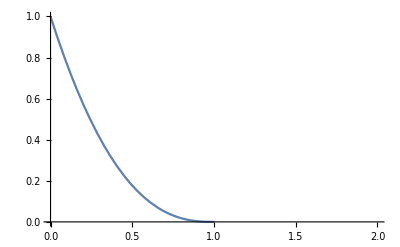

```mathematica
Plot[pot[x, 1.0, 1.0], {x, 0, 2}]
```

```mathematica
potinverse[x_, rc_, a_] = If[x<rc, pot[x,rc, a] , 0]
```

If[x<rc,pot[x,rc,a],0]

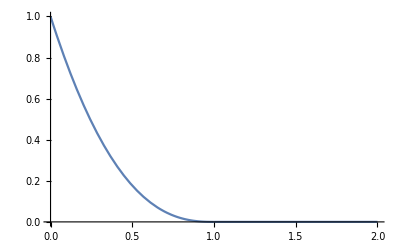

```mathematica
Plot[potinverse[x, 1.0, 1.0], {x, 0, 2}, PlotRange->Full]
```

```mathematica
potsmoothed[x_, rc_, rs_, a_, delta_] = If [x < rc (1-delta), pot[x, rc, a], If[x < rs, smoothingpolynomial[x, rc, rs, a, delta], 0]]
```

If[x<(1-delta) rc,pot[x,rc,a],If[x<rs,smoothingpolynomial[x,rc,rs,a,delta],0]]

```mathematica
symlog={Function[x,Sign[x] (Log[Abs[x]+1])],Function[y,Sign[y] (Exp[Abs[y]]-1)]};
```

```mathematica
Manipulate[Plot[{potsmoothed[x, 1.0, 2.0, 1.0, δ], potinverse[x, 1.0, 1.0]}, {x, 0, 2}, PlotRange->Full, ScalingFunctions->symlog, PlotLegends->{"Extended Hertzian", "Original Hertzian"}], {δ, 0, 0.3}]
```

Plot::sclfn: The scaling function symlog cannot be used to scale coordinates.

```mathematica
potsmoothed[1.5, 1.0, 2.0, 1.0, 0.01]
```

0.00547375

```mathematica
potsmoothed[0.1, 1, 2.0, 1.0, 0.01]
```

0.768433 coeff

```mathematica
potadded[x_, rc_, rs_, a_, b_] = potinverse[x, rc, a] + potinverse[x, rs,  b]
```

If[x<rc,pot[x,rc,a],0]+If[x<rs,pot[x,rs,b],0]

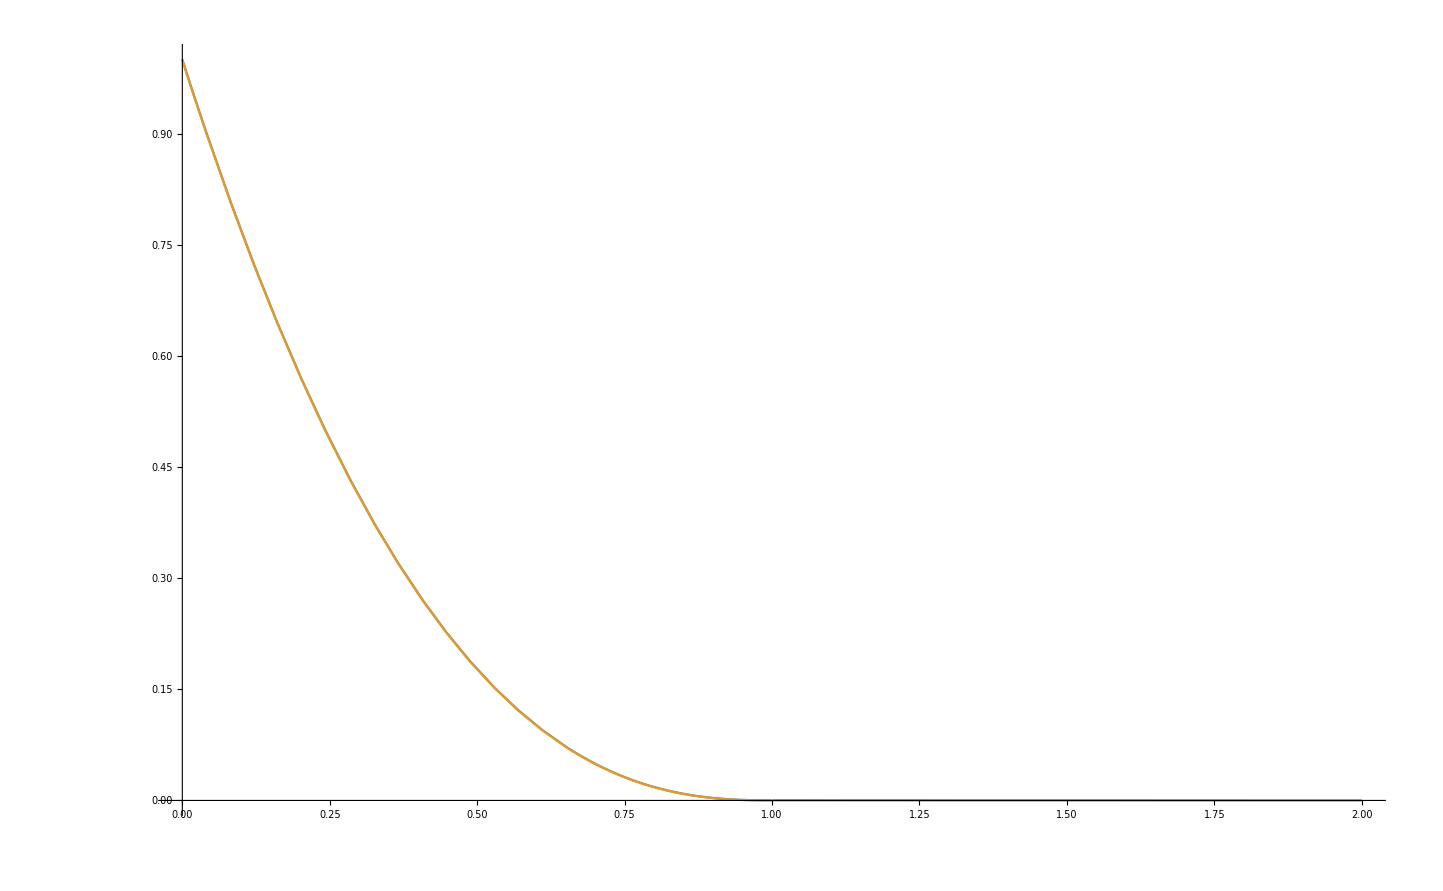

```mathematica
Plot[{potadded[x, 1.0, 2.0, 1, 10^-3], pot[x, 1.0, 1.0]}, {x, 0, 2}]
```

```mathematica
potinverse[1, 1, 1, 1]
```

potinverse[1,1,1,1]

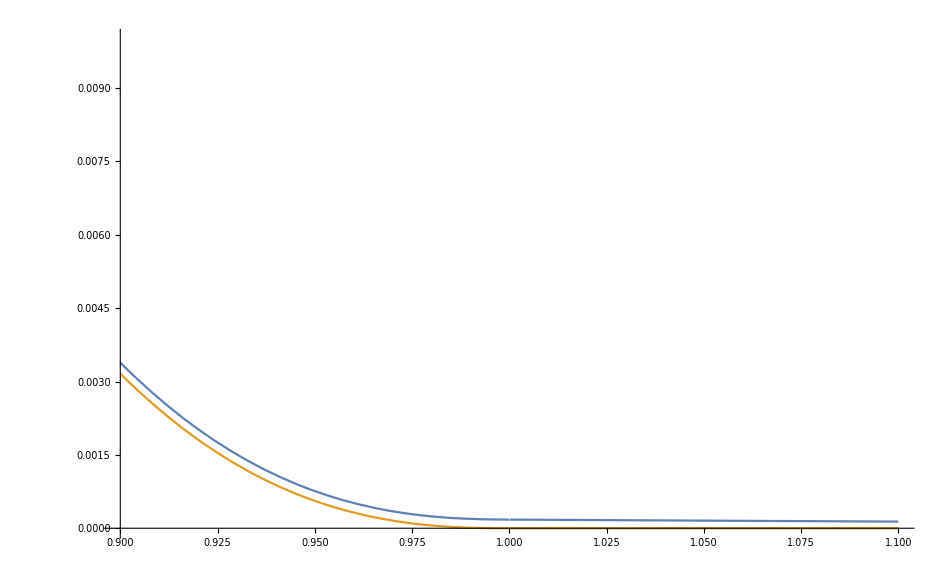

```mathematica
Plot[{potadded[x, 1.0, 2.0, 1, 10^-3], potinverse[x, 1.0, 1.0]}, {x, 1-10^-1, 1+10^-1}, PlotRange->{0, 10^-2}]
```

```mathematica
potadded[1.0, 1.0, 2.0, 1, 10^-3]
```

0.000176777

```mathematica
Plot[{D[potadded[x, 1.0, 2.0, 1, 10^-3], x], D[potinverse[x, 1.0, 1.0],x]}, {x, 0, 2}, PlotRange->{0, 10^-2}]
```

General::ivar: 0.0000408571 is not a valid variable.

General::ivar: 0.0408572 is not a valid variable.

General::ivar: 0.0816735 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
D[fevaled[x],x]
```

If[x<1.,3.75 (1-1. x)^0.5,0]+If[x<2.,0.0009375 (1-0.5 x)^0.5,0]

```mathematica
Plot[f[r], {r,0,2}]
```

General::ivar: 0.0000408571 is not a valid variable.

General::ivar: 0.0408572 is not a valid variable.

General::ivar: 0.0816735 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

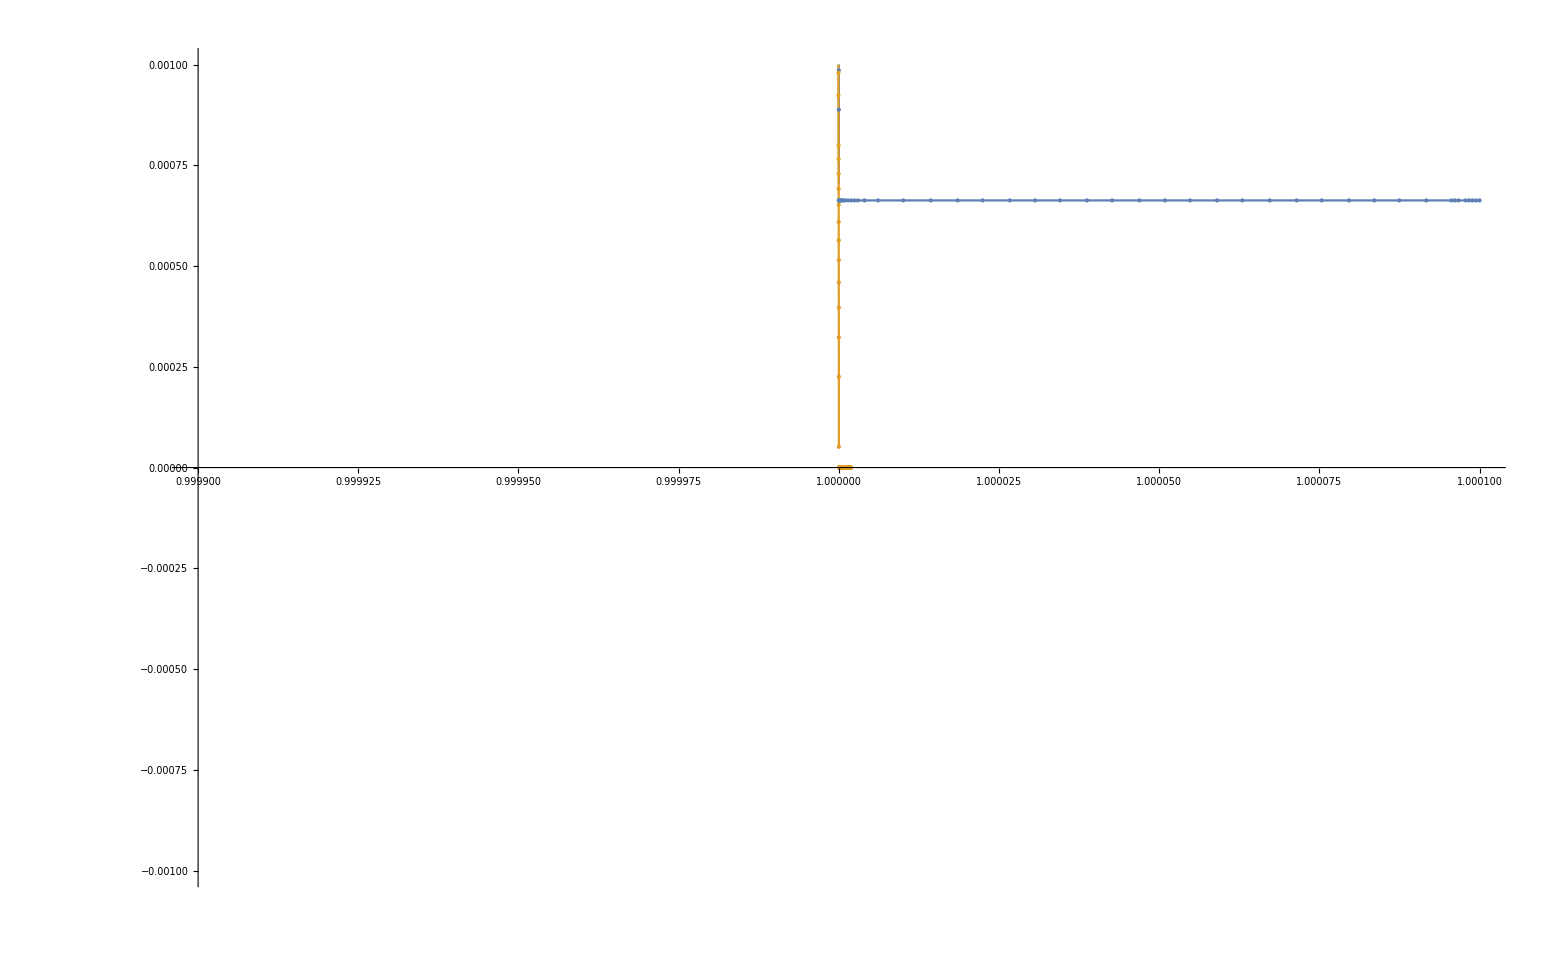

```mathematica
Plot[{If[x<1.,3.75 (1-1. x)^0.5,0]+If[x<2.,0.0009375 (1-0.5 x)^0.5,0], potdprime[x, 1., 1]}, {x, 1-10^-4,1+10^-4}, PlotRange->{-10^-3, 10^-3}, Mesh->All, MaxRecursion->15]
```

```mathematica
f[x_] = D[potadded[x, 1.0, 2.0, 1, 10^-3],x]
```

```mathematica
fevaled[x_] = If[x<1.,-2.5 (1-1. x)^1.5,0]+If[x<2.,-0.00125 (1-0.5 x)^1.5,0]
```

If[x<1.,-2.5 (1-1. x)^1.5,0]+If[x<2.,-0.00125 (1-0.5 x)^1.5,0]

```mathematica
potprime[x, 1, 1]
```

-2.5 (1-x)^1.5

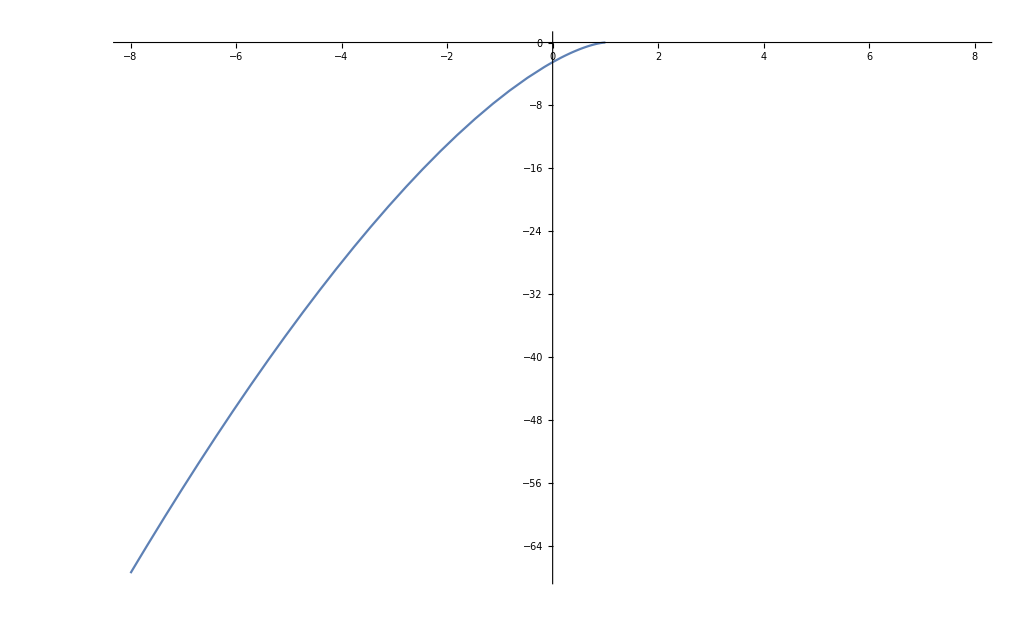

```mathematica
Plot[-2.5 (1-x)^1.5,{x,-8,8}]
```

```mathematica
Derivative[1,0,0][pot][x,2.,1/1000]
```

-0.00125 (1-0.5 x)^1.5

```mathematica
Function[x,D[potadded[x,1.,2.,1,1/10^3], x]]
```

Function[x,∂_x potadded[x,1.,2.,1,1/10^3]]

```mathematica
potadded[x]
```

potadded[x]

```mathematica
ReleaseHold[[D[potadded[x, 1.0, 2.0, 1, 10^-3],x]]]
```

Part::pkspec1: The expression If[x<1.,pot^(1,0,0)[x,1.,1],0]+If[x<2.,pot^(1,0,0)[x,2.,1/1000],0] cannot be used as a part specification.

ReleaseHold⟦If[x<1.,pot^(1,0,0)[x,1.,1],0]+If[x<2.,pot^(1,0,0)[x,2.,1/1000],0]⟧

```mathematica
po
```

```mathematica
pot[1,1,1]
```

0.

```mathematica
Derivative[1,0,0][pot][x,1.,1]
```

-2.5 (1-1. x)^1.5

```mathematica
SetAttributes[Evaluate[D[potadded[x, 1.0, 2.0, 1, 10^-3],x]], NHoldAll]
```

SetAttributes::sym: Argument If[x<1.,pot^(1,0,0)[x,1.,1],0]+If[x<2.,pot^(1,0,0)[x,2.,1/1000],0] at position 1 is expected to be a symbol.

SetAttributes[If[x<1.,pot^(1,0,0)[x,1.,1],0]+If[x<2.,pot^(1,0,0)[x,2.,1/1000],0],NHoldAll]

```mathematica
pot
```